```mathematica
Clear["Global`*"]
```

# Bayesian Model of distance perception from ocular convergence

## Peter Scarfe and Paul Hibbard (2025)

## Code to plot and analyse the response distribution data

## Loads in the peaks of the simulated response distributions. Fits a surface to the data. Finds the best fitting noise value to the Viguier data. Handles all plotting.

## Data Loading

### We load in the data that has been generated for the peaks of the response distributions.

```mathematica
(* List all of the data files for the response distributions *)
allDataFiles=FileNames["allPeaksForResponseDistributions*.mx",NotebookDirectory[]<>"Response Distribution Peaks/"];
```

```mathematica
(* Number of simulations *)
numFiles=Length[allDataFiles];
numSims=10000;
numSimsAll=numSims*numFiles;
```

```mathematica
(* Import the data amnd get its size *)
peakPosAllTable=Table[Import[allDataFiles[[i]]],{i,1,numFiles}];
Dimensions@peakPosAllTable
```

{10,7,9,10000}

```mathematica
(* Collapse ovber the first dimension and get dimensions *)
peakPosAll=Flatten[peakPosAllTable,{{2},{3},{1,4}}];
{numSig,numDist,numSamples}=Dimensions@peakPosAll
```

{7,9,100000}

```mathematica
(* Noise level indices *)
noiseLevels=Range[numSig]
```

{1,2,3,4,5,6,7}

```mathematica
(* Noise levels *)
sigmaValuesRad=Range[0.25, 1.75, 0.25]*Degree;
sigmaValuesDeg=sigmaValuesRad/Degree;
noiseMat=ConstantArray[sigmaValuesDeg,numDistances];
```

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[{0.25,0.5,0.75,1.,1.25,1.5,1.75},numDistances].

## Setup Parameters

### Various setup parameters for use later.

```mathematica
(* Trigger saving or not *)
doSaving=True;
```

```mathematica
(* Font sizes *)
frameFS=18;
titleFS=25;
```

```mathematica
(* Distances *)
distanceValues=Range[20,100,10];
numDistances=Length@distanceValues;
```

```mathematica
(* Viguier Data *)
vigDataMean={21, 30.5, 37.5, 49.5, 55.5};
vigDataX={20, 30, 40, 60, 80};
vigDataUpper={24, 34.5, 41, 56, 68.5}-vigDataMean;
vigDataLower= vigDataMean-{18, 27, 34, 43, 43};
```

```mathematica
(* Maximum distance in which a peak can be found *)
maxDistance=400;
```

```mathematica
legendLabels=Table[Row[{b,"cm"}],{b,Round@distanceValues}];
```

```mathematica
(* Funciton to grab the default color scheme *)
chartColors[chartType_,plotTheme_]:=("ChartDefaultStyle"/.(Method/.Charting`ResolvePlotTheme[plotTheme,chartType]))/.Directive[x_,__]:>x
```

## Get bin counts for the data as a histogram

### We get data histograms of the data and get the maximum bin. We then use this for the seed for the peaking finding for the distribution fit by Mathematica FindDistribution function.

```mathematica
(* Bins to for the histograms *)
theBins={0,150,150/100};
```

```mathematica
(* The maximum and its bin *)
histPosMax=Table[
{bins,counts}=HistogramList[peakPosAll[[i,ii,All]],theBins];
maxHeight=Max[counts];
maxPosition=Mean[bins[[First@Position[counts,maxHeight][[1]];;First@Position[counts,maxHeight][[1]]+1]]];
{maxPosition,maxHeight}
,{i,1,numSig},{ii,1,numDist}];
Dimensions@histPosMax
```

{7,9,2}

```mathematica
(* Get all of the max positions and values *)
maxPosGuess=Table[histPosMax[[i,ii,1]],{i,1,numSig},{ii,1,numDist}];
maxValueGuess=Table[histPosMax[[i,ii,2]],{i,1,numSig},{ii,1,numDist}];
```

```mathematica
(* Same again but a way avoiding table *)
maxPosGuess2={#[[All,All,1]]}&@histPosMax;
maxValueGuess2={#[[All,All,2]]}&@histPosMax;
```

## Find best fitting distributions for all of the response distribution histograms

### We find the best fitting distribution using the Find Distribution function. One could worry that the distributions found not not match the data. We visualise all of the data to do this. We also fit smooth kernel distributions to the data as well and compare the results.

```mathematica
(* Find best fitting distributions *)
estDistribsRespDistrib=ParallelTable[
FindDistribution[peakPosAll[[i,ii,All]],PerformanceGoal->"Quality"],{i,1,numSig},{ii,1,numDist}];
Dimensions@estDistribsRespDistrib
```

{7,9}

```mathematica
(* Convert to PDF *)
estDistribsRespDistribPDF=Table[PDF[estDistribsRespDistrib[[i,ii]],y],{i,1,numSig},{ii,1,numDist}];
Dimensions@estDistribsRespDistribPDF
```

{7,9}

```mathematica
(* Alternatively could fit smooth kernal distributions *)
estDistribsRespSmoothDistrib=ParallelTable[SmoothKernelDistribution[peakPosAll[[i,ii,All]],PerformanceGoal->"Quality"],{i,1,numSig},{ii,1,numDist}];
```

## Find the peaks of these distributions

### We use the x-position of the max of the histograms as a guess as to the position of the maximum in the FindMaximum search to get the peaks of the fitted PDF’s to the response distributions.

```mathematica
(* Find the peaks of the response distributions: with the parametric distributions *)
distribPeakTable=ParallelTable[FindMaximum[PDF[estDistribsRespDistrib[[i,ii]],x],{x,maxPosGuess[[i,ii]],0,400},Method-> "PrincipalAxis",AccuracyGoal->6,MaxIterations->100],{i,1,numSig},{ii,1,numDist}];
```

```mathematica
(* Tuples of peaks and positions *)
peakValueAndPosRev=Table[{#[[1]],#[[2,1,2]]}&/@subList,{subList,distribPeakTable}];
peakValueAndPos=Table[Reverse[peakValueAndPosRev[[i,ii]]],{i,1,numSig},{ii,1,numDist}];
Dimensions@peakValueAndPos
```

{7,9,2}

```mathematica
peakDistMat=peakValueAndPos[[All,All,1]]//Transpose;
```

```mathematica
(* Find the peaks of the response distributions: with the smooth kernal distributions *)
distribPeakSmoothTable=ParallelTable[FindMaximum[PDF[estDistribsRespSmoothDistrib[[i,ii]],x],{x,maxPosGuess[[i,ii]],0,400},Method-> "PrincipalAxis",AccuracyGoal->6,MaxIterations->100,WorkingPrecision->30],{i,1,numSig},{ii,1,numDist}];
```

```mathematica
(* Get the x values of the peak for both methods *)
peakXValues=distribPeakTable/. {_,sol_}:>(x/. sol);
peakXValuesSmooth=distribPeakSmoothTable/. {_,sol_}:>(x/. sol);
```

```mathematica
(* Pair for plotting *)
setsOfPeaks=Transpose[{Flatten@peakXValues,Flatten@peakXValuesSmooth}];
```

```mathematica
(* Linear regression *)
lm=LinearModelFit[setsOfPeaks,x,x]
```

FittedModel[…]

### Plot to compare the two methods and fit a linear regression . The two methods provide virtually identical results, so we stick with the FindDistribution results which was the first method we used. The linear regression is effectively near identical to the unity line. We can therefore be assured that our fits are good and represent the data well.

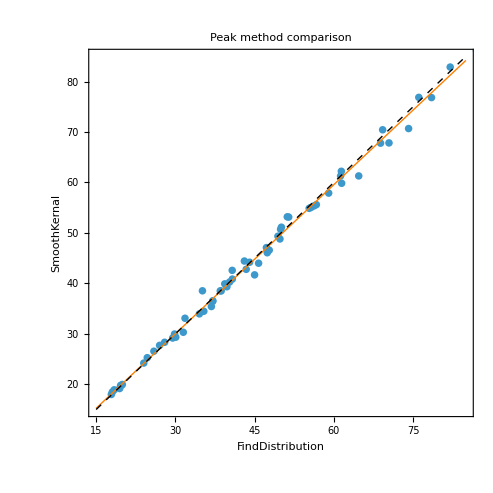

```mathematica
peakCompPlot=ListPlot[setsOfPeaks,PlotRange->{{15,85},{15,85}},AspectRatio->1,Frame->True,BaseStyle->14,PlotLabel->"Peak method comparison",FrameLabel->{"FindDistribution","SmoothKernal"}];
linearPeaksFit=Plot[lm[x],{x,15,85},PlotStyle->{Thick,Orange}];
Show[{peakCompPlot,linearPeaksFit,Graphics[{Dashed,Black,Line[{{15,15},{85,85}}]}]}]
```

```mathematica
(* Tuples of peaks and positions *)
peakValueAndPosRev=Table[{#[[1]],#[[2,1,2]]}&/@subList,{subList,distribPeakTable}];
peakValueAndPos=Table[Reverse[peakValueAndPosRev[[i,ii]]],{i,1,numSig},{ii,1,numDist}];
```

## Plot example histogram of response distributions

### We plot example histograms for one noise level for all distances and overlay the peaks. This is the peak based in the bin counts and they are used as the guess for thew maximum search for the parametric distributions.

```mathematica
(* Example noise to plot *)
exampleNoiseNum=4;
```

```mathematica
(* Get the maximums used for this example *)
exampleMaxs=histPosMax[[exampleNoiseNum,All]];
```

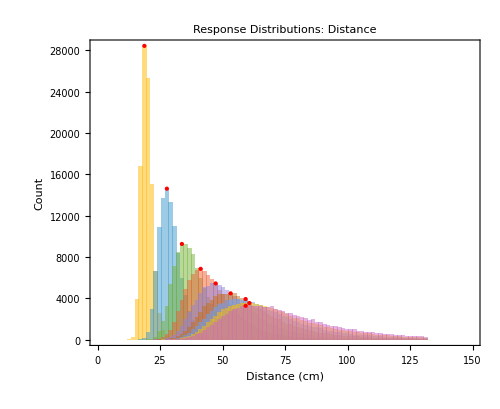

```mathematica
(* Plot example h *)
histRespDistribExample=Histogram[peakPosAll[[exampleNoiseNum,All,All]],theBins,"Count",
FrameLabel-> {"Distance (cm)","Count"},
PlotLabel->Style["Response Distributions: Distance",Black,FontSize->titleFS], 
ImageSize->500, BaseStyle->{FontSize-> 13.5},
FrameStyle->Directive[Black,Thickness[0.0024],FontSize->frameFS], 
Frame->True,ImagePadding->All,AspectRatio->0.82,
PlotRangeClipping->False,Epilog->{PointSize[Medium],Red,Point[exampleMaxs]}]
```

## Plot of response distributions for the paper

### We drop the 20cm distance for the plot to be consistent with the rest of the figures in the paper. The 20cm is use for the surface fitting etc to provide more data to find a fit.

```mathematica
(* Plot the estimate distributions *)
examplePDFs=estDistribsRespDistribPDF[[exampleNoiseNum,2;;9]];
examplePDFpeaksRev=peakValueAndPos[[exampleNoiseNum,2;;9]];
```

```mathematica
(* Plot the histogram example again but the PDF version *)
exapleHistAlone=Histogram[peakPosAll[[exampleNoiseNum,2;;9,All]],{0,150,150/100},"PDF",Frame->True];
```

```mathematica
(* Make the respoinse distribution plot for the paper *)
pdfsRespDistribExample=Quiet@Plot[examplePDFs,{y,0,150},PlotRange->{{0,150},{0,0.11}},
FrameLabel-> {"Distance (cm)",TraditionalForm[p(Subscript[OverHat[D],R]|D )]},
PlotLabel->Style["Response Distributions: Distance",Black,FontSize->titleFS], 
PlotStyle->Thread[{Thickness[0.005],chartColors[Histogram,$PlotTheme]}],
ImageSize->500, BaseStyle->{FontSize-> 13.5},
FrameStyle->Directive[Black,Thickness[0.0024],FontSize->frameFS], 
Frame->True,ImagePadding->All,AspectRatio->0.82,
PlotRangeClipping->False,Epilog->{PointSize[Large],Red,Point[examplePDFpeaksRev]},
PlotLegends->Placed[LineLegend[legendLabels[[2;;9]],LegendFunction->Framed],{0.85,0.67}]];
```

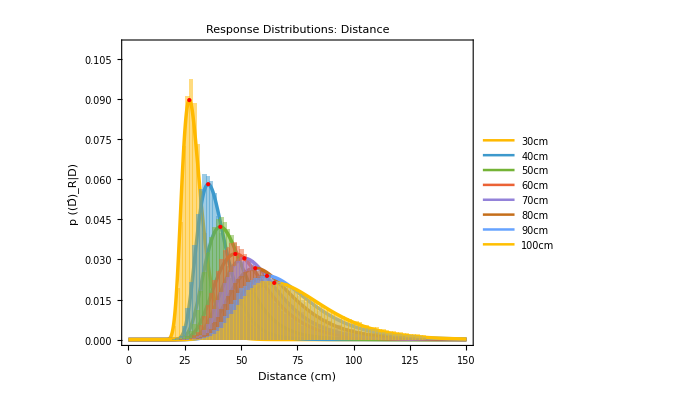

```mathematica
respDistribExample=Show[{pdfsRespDistribExample,exapleHistAlone}]
```

```mathematica
(* Save the graph if we want *)
If[doSaving,Export[StringJoin[NotebookDirectory[],"respDistribExample.jpg"],respDistribExample, ImageResolution->500],Nothing];
```

## Manipulate to all visualisation of all the data

```mathematica
(*Manipulate a ListPlot with adjustable subset range*)
Manipulate[

If[nnn===1,theStyle=Darker@Gray,theStyle=Opacity[0]];
If[nnn===1,theDotStyle=Red,theDotStyle=Opacity[0]];

exampleHistAlone=Histogram[peakPosAll[[n,All,All]],{0,150,150/100},"PDF",
PlotRange->{{0,150},{0,All}},
FrameLabel-> {"Distance (cm)","Probability"},
PlotLabel->Style["Response Distributions: Distance",Black,FontSize->titleFS],
ImageSize->600, BaseStyle->{FontSize-> 13.5},
FrameStyle->Directive[Black,Thickness[0.0024],FontSize->frameFS], 
Frame->True,ImagePadding->All,AspectRatio->0.82,
PlotRangeClipping->False];

pdfsRespDistribExample=Quiet@Plot[estDistribsRespDistribPDF[[n,All]],{y,0,150},
PlotRange->{{0,150},{0,All}},
FrameLabel-> {"Distance (cm)","Probability"},
PlotLabel->Style["Response Distributions: Distance",Black,FontSize->titleFS], 
PlotStyle->theStyle,
ImageSize->600, BaseStyle->{FontSize-> 13.5},
FrameStyle->Directive[Black,Thickness[0.0024],FontSize->frameFS], 
Frame->True,ImagePadding->All,AspectRatio->0.82,
PlotRangeClipping->False,
Epilog->{PointSize[Large],theDotStyle,Point[peakValueAndPos[[n,All]]]}];

Show[{pdfsRespDistribExample,If[nn===1,exampleHistAlone,Nothing]}]
,
{{n,1,Style["Noise Level", FontSize->14]},noiseLevels},
{{nn,1,Style["Do Histogram", FontSize->14]},{0,1}},
{{nnn,1,Style["Do PDF's", FontSize->14]},{0,1}}]
```

## Fitting the surface

### We plot the peaks of the response distributions and fit a surface to these. The surface is simply a summary of the data for later steps.

```mathematica
(* Format the data for plotting the peaks of the response distributions for all of the sigma values and distances *)
surfTable=Table[Transpose[{distanceValues,noiseMat[[All,i]],peakDistMat[[All,i]]}],{i,1,7}];
```

```mathematica
(* A quadrative surfces fits the data well and is low enough order so as not to visually overfit the data *)
quad=LinearModelFit[Flatten[surfTable,1],{1,x,y,x^2,x y,y^2},{x,y}]
quad["AdjustedRSquared"]
```

FittedModel[…]

0.995113

### We minimise the fit of the Viguier data to the fitted surface. In the surface plot below you can imagine this as sliding the Viguier data up and down the “Vergence Noise” axis to see when it has minimal distance from the surface. This is estimating the noise value that would best account for the data.

```mathematica
(* Find the best fitting noise *)
sol=Minimize[Total@(Table[quad[vigDataX[[n]],z],{n,1,5}]-vigDataMean)^2,z];
bestNoise=z/.Last@sol
vigData3D=Transpose[{vigDataX,ConstantArray[bestNoise,5],vigDataMean}];
```

0.793242

```mathematica
(* Plot the response distribution surface, the fit, and the Viguier data in its best fit position *)
allPoints=ListPointPlot3D[surfTable,AxesLabel->{"Physical Distance (cm)","Vergence noise (degrees)","Estimated Distance (cm)"},LabelStyle->Directive[Black,15]];
planeFit=Plot3D[quad[x,y],{x,20,100},{y,0.25, 1.75},PlotStyle->{Opacity[0.5]}];
vigPlot3D=ListPointPlot3D[vigData3D,PlotStyle->Black];
```

```mathematica
noiseSurfacePlot=Show[allPoints,planeFit,vigPlot3D,ImageSize->800]
```

-Graphics3D-

```mathematica
(* Save the graph if we want *)
If[doSaving,Export[StringJoin[NotebookDirectory[],"noiseSurfacePlot.jpg"],noiseSurfacePlot,ImageResolution->500],Nothing];
```

## Plotting a slice of the surface and the Viguier data

### We plot the Viguier data and a slice through the surface at the best fitting noise value. We also plot 95% confidence interval’s around the model and calculate R-Squared of the surface slice to the data.

```mathematica
(* Distance values for this plot *)
distanceValues2=N@{20,30, 40, 50, 60, 70, 80};
plottingRange={15,95};
```

```mathematica
(* Extract the equation using the best fitting noise value *)
quadEq=Normal[quad];
vigFit=quadEq/.y->bestNoise;
```

```mathematica
(* Plot the single prediction 95% error bads for the surface slice i.e. error around the model *)
vigFitErr=Plot[Evaluate[{quad["SinglePredictionBands"][[1]]/. y->bestNoise,quad["SinglePredictionBands"][[2]]/. y->bestNoise}],{x,20,80},PlotStyle->Blend[{LightBlue,Blue},0.4],Filling->{1->{2}}];
```

```mathematica
(* Unity line *)
unityLineVig=ListLinePlot[Transpose[{distanceValues2,distanceValues2}],PlotRange->plottingRange,PlotStyle->{Black, Dashed,Thickness[0.006]}];
```

```mathematica
(* Viguier data and errorbars *)
vigWithError=Table[Around[vigDataMean[[i]],{vigDataLower[[i]],vigDataUpper[[i]]}],{i,1,Length@vigDataMean}];
```

```mathematica
(* Predicted Viguier Data and the R^2 for the model fit *)
predVig=Table[quad[vigDataX[[i]],bestNoise],{i,1,Length@vigDataX}];
rSquaredOfFit=1-Total[(vigDataMean-predVig)^2]/Total[(vigDataMean-Mean[vigDataMean])^2]
```

0.917112

```mathematica
(* Plot the Viguier fit *)
fitPlot=Plot[vigFit,{x,20,80},Frame->True,PlotStyle->Thickness[0.006],
AspectRatio->1,ImageSize->500,
Frame->True,FrameStyle->Directive[Black,Thickness[0.0024],FontSize->frameFS],
FrameLabel-> {"Physical Distance (cm)","Estimated Distance (cm)"},
PlotLabel->Style["Viguier et al. (2001)",Black,FontSize->titleFS],PlotRange->plottingRange,BaseStyle->{FontSize-> 16},
Epilog->{Text[Style[Row[{Superscript["R","2"]," = ",NumberForm[rSquaredOfFit,2]}],21],Scaled[{0.15,0.92}]]}];
```

```mathematica
(* Viguier Plot with error bars *)
vigData=Transpose[{vigDataX, vigWithError}];
vigDataAll=Transpose[{vigDataX, vigDataMean,vigDataUpper,vigDataLower}];
vigPlot=ListLinePlot[vigData,PlotMarkers->Graphics[Disk[],ImageSize->15], PlotStyle->{Black,Thickness[0.006]},IntervalMarkersStyle->{Black,Thickness[0.005]},PlotRange->plottingRange];
```

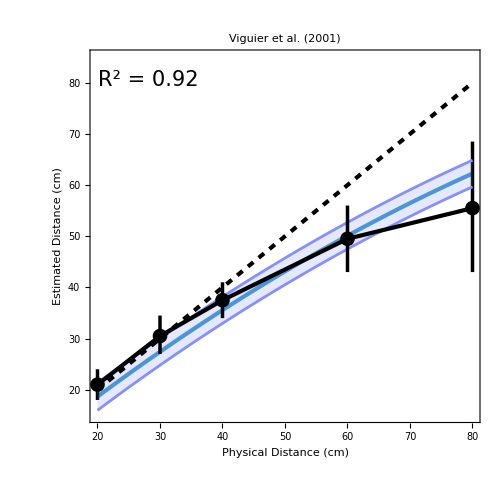

```mathematica
(* Overlay all of the component graphs *)
finalVigPlot=Show[fitPlot,vigFitErr,vigPlot,unityLineVig,PlotRange->{15,85}]
```

```mathematica
(* Save it we want *)
If[doSaving,Export[StringJoin[NotebookDirectory[],"finalVigPlot.jpg"],finalVigPlot,ImageResolution->500],Nothing];
```

## Plot the data used to fit the surface

### This plot is not used in the paper. It is just another way of plotting the same data. It is of similar style to the plot of the peaks of the posteriors for various noise levels.

```mathematica
lineTable=Table[Transpose[{distanceValues,peakDistMat[[All,i]]}],{i,1,7}];
```

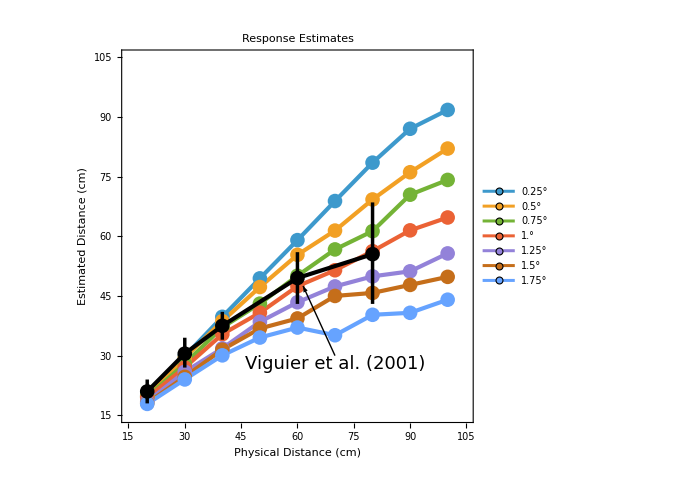

```mathematica
sigmaLegendLabels=Table[Row[{b, "°"}],{b,N[Range[0.25, 1.75, 0.25]]}];
theLinePlot=ListLinePlot[lineTable,PlotRange->{{15,105},{15,105}},
PlotStyle->Thickness[0.006],PlotMarkers->Graphics[Disk[],ImageSize->15],
AspectRatio->1,ImageSize->500,
Frame->True,FrameStyle->Directive[Black,Thickness[0.0024],FontSize->frameFS],
FrameLabel-> {"Physical Distance (cm)","Estimated Distance (cm)"},
PlotLabel->Style["Response Estimates",Black,FontSize->titleFS],
BaseStyle->{FontSize-> 16},PlotLegends->Placed[LineLegend[sigmaLegendLabels,LegendFunction->Framed],{0.135,0.72}],
PlotRangeClipping->False,
Epilog->{Thick,Arrow[{{70,30},{vigDataX[[4]]+1.5,vigDataMean[[4]]-2}}],Text[Style["Viguier et al. (2001)",18],{70,28}]}];
respEsts=Show[theLinePlot,vigPlot]
```

```mathematica
(* Save it we want *)
If[doSaving,Export[StringJoin[NotebookDirectory[],"respEsts.jpg"],respEsts, ImageResolution->500],Nothing];
```